```mathematica
Options[svgExport]={"CommentString"->"Created by Mathematica",AspectRatio->Automatic,Background->Automatic};
Clear[svgExport];
svgExport[name_String,gr_,opts:OptionsPattern[]]:=Module[{svgCode=StringReplace[ExportString[First@ImportString[ExportString[gr,"PDF",Background->OptionValue[Background]],"PDF"],"SVG",Background->OptionValue[Background]],"<svg "->"<svg "<>If[OptionValue[AspectRatio]===Full," preserveAspectRatio='none' "," "]]&[ToString/@ImageDimensions[Rasterize[Show[gr,ImagePadding->0],"Image"]]]},Export[name,StringReplace[svgCode,RegularExpression["(<svg\\b[^>]*>)"]:>"$1"<>"\n<!-- ***Exported Comment***\n"<>OptionValue["CommentString"]<>"\n***Exported Comment*** -->"],"Text"]]

edges = {1<->2,1<->3,3<->4,3<->5,5<->6,5<->7,7<->8};
coords = {{0,0},{0,-1},{1,0},{1,-1},{2,0},{2,-1},{3,0},{3,-1}};
names = {1,1,2,2,3,3,4,4};
Graph[edges, VertexCoordinates->coords,VertexSize->Medium,ImageSize->400,
VertexLabels->Thread[Range[8]->(Placed[Style[#,12,"Panel",Background->None],Center]&/@names)]]
```

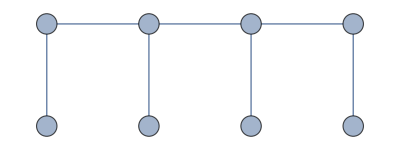

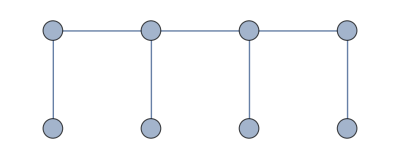
```mathematica
svgExport["/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/hmm_graph_example.svg",-Graphics-, AspectRatio->Full]
```

/Users/elvis/Documents/DSI/courses/content/stochastic-approximations/images/hmm_graph_example.svg